# Dielectric and permeability tensor

## 1. Global constants

```mathematica
hbar=1.0545718176461565*10^-27;
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
mp=1.67262192369*10^-24;
A=1;Z=1;Ye=1;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
c=29979245800.0;
σT=8*π/3*e^4/(c^4 me^2);
κT=σT/mp;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
km=10^5;
αF=e^2/(hbar c);
BQ=me^2*c^3/e/hbar;
```

## Special functions

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
C0[a_]:=1/a-Exp[a]*ExpIntegralE[1,a];
C1[a_]:=(1+a)*Exp[a]*ExpIntegralE[1,a]-1;
radian[x_]:=x/180*π;
```

## Blackbody function

```mathematica
(*for flux, we need to condifer the projection*)
2π*NIntegrate[Sin[θ]*Cos[θ],{θ,0,π/2}]
```

3.14159

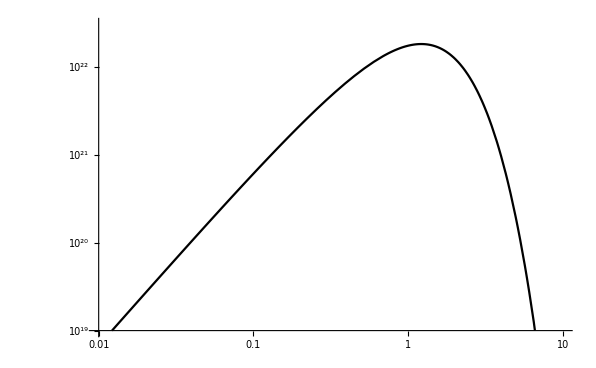

```mathematica
Planck[Es_,T_]:=2*hbar*2*π*(Es*kev2erg/hbar/2/π)^3/c^2*1/(Exp[(Es*kev2erg)/(kb*T)]-1);
Tp=5*10^6;
LogLogPlot[π*Planck[Es,Tp]/hbar/2/π*kev2erg,{Es,0.01,10},PlotRange->{{0.01,10},{10^19,3*10^22}},Background->White,PlotTheme->"Monochrome"]
```

## Gaunt factors

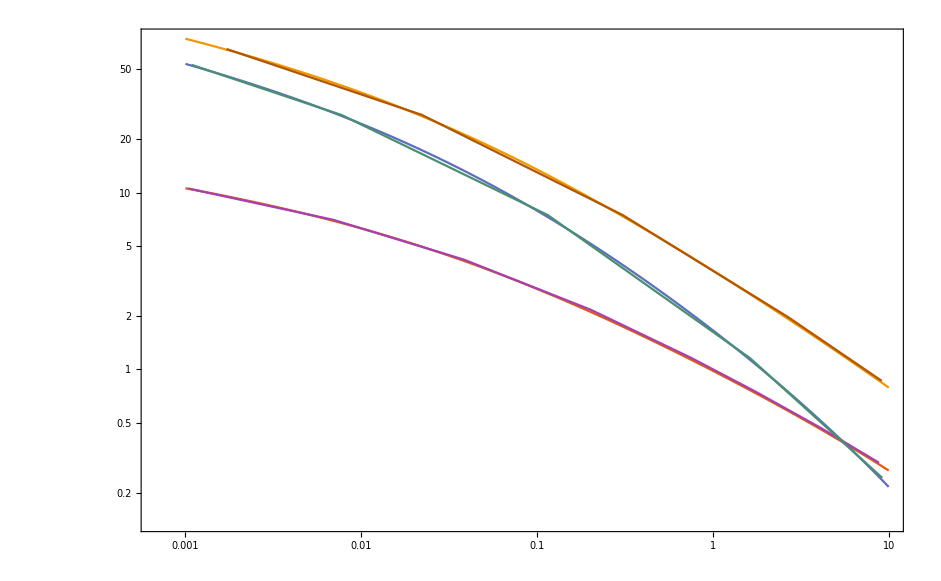

```mathematica
gL[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*C1[r2*Exp[2 x]],{x,-Infinity,Infinity}]
gP[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*2*r2*Exp[2x]C0[r2*Exp[2 x]],{x,-Infinity,Infinity}]
Ekev=logspace[-3,1,100];
Ec=Ekev*kev2erg;
ω=Ec/hbar;
B=10^13;
ωc=e*B/me/c;
T=10^6;
r1=hbar*ωc/(kb*T);
r2=ω/ωc;
B1=5*10^14;
ωc1=e*B1/me/c;
r11=hbar*ωc1/(kb*T);
r21=ω/ωc1;
gaunt=gP[r1,r2];
gaunt1=gL[r1,r2];
gaunt2=gL[r11,r21];
data=Transpose@{Ekev,gaunt};
data1=Transpose@{Ekev,gaunt1};
data2=Transpose@{Ekev,gaunt2};
SetDirectory[NotebookDirectory[]];
list=Import["./gp1.csv"];
list1=Import["./gl1.csv"];
list2=Import["./gl2.csv"];
ListLogLogPlot[{data,data1,data2,list,list1,list2},PlotRange->All,Joined->True,PlotTheme->"Scientific",Background->White]
```

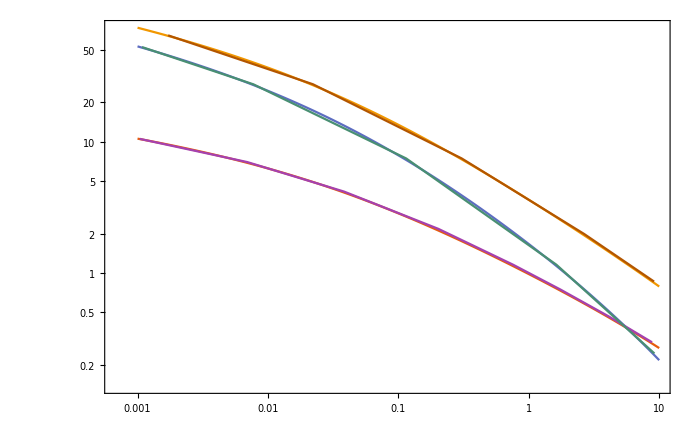
```mathematica
-Graphics--Graphics-
```

#### Note that here I use the solutions of Nagel 1980, not the results in Meszaros 1992, which is

Note that the a+- is wrong, the correct one is

## Free-free opacity in Ho & Lai 2003

```mathematica
energy[Es_,B_,ρ_]:=Module[{Ece,Eci,Epe,Epi,ue,ui,ve,vi},
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
{Ece,Eci,Epe,Epi,ue,ui,ve,vi}
]
energy[1,10^14,1]
```

{1157.68,0.63049,0.0287117,0.000670045,1.34021×10^6,0.397518,0.00082436,4.4896×10^-7}

```mathematica
-Graphics-
-Graphics-
```

```mathematica
free1[Es_,B_,ρ_,T_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,α0,gl,gp,y1,y2,ωci,νre,νep,νem,νe0,νip,νim,νi0,ffe1,ffi1,ffe2,ffi2,ff1,ff2},
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x]^2]*C1[y2*Exp[2 x]],{x,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x]^2]*2*y2*Exp[2x]C0[y2*Exp[2 x]],{x,-Infinity,Infinity}];
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;
ffe1=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*gl+(ω^2/((ω-1*ωc)^2+νem^2))em1*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e01*gp);
ffi1=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*gl+(ω^2/((ω+1*ωci)^2+νim^2))em1*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e01*gp);
ffe2=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*gl+(ω^2/((ω-1*ωc)^2+νem^2))em2*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e02*gp);
ffi2=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*gl+(ω^2/((ω+1*ωci)^2+νim^2))em2*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e02*gp);


ff1=ffe1+ffi1;
ff2=ffe2+ffi2;
{ff1,ff2}

]
```

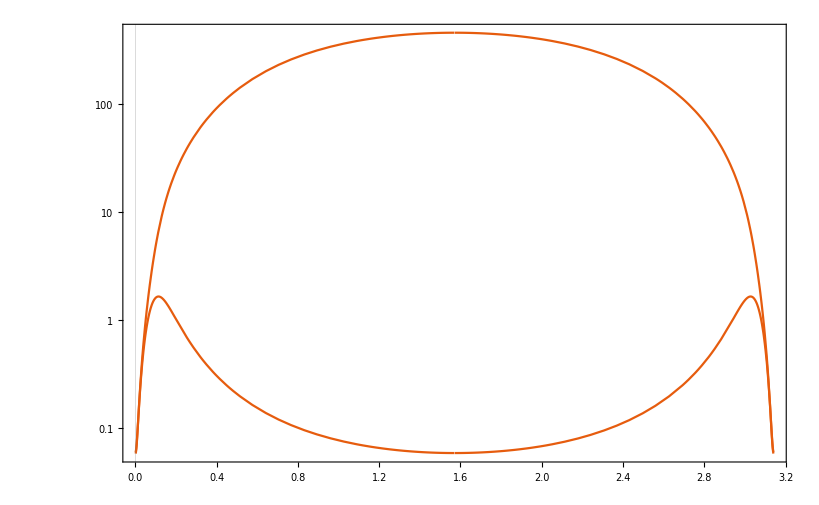

```mathematica
B=10^13;ρ=200;T=10*10^6;Es=1;
LogPlot[free1[Es,B,ρ,T,θb],{θb,0.001,π-0.001},PlotRange->Full,PlotTheme->"Scientific",Background->White]
```

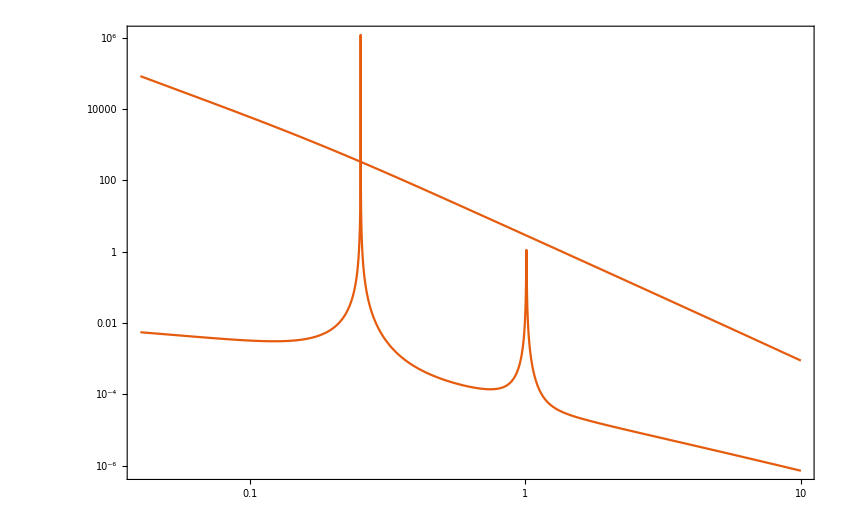

```mathematica
B=4*10^13;ρ=1;T=10^6;θb=π/3;
LogLogPlot[free1[Es,B,ρ,T,θb],{Es,0.04,10},PlotRange->Full,PlotTheme->"Scientific",Background->White]
```

#### The results are consistent with Ho & Lai 2003

## Aint

```mathematica
Aint[Es_,B_,ρ_,T_,θ_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,Ap1,Am1,A01,Ap2,Am2,A02,Ap,Am,A0},
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
(*a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);*)
(*turn off the vacuum*)
a=1;
q=0;
m=0;
r=1+m/a Sin[θ]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θ]^2/Cos[θ];
K1=β(1-(1+r/β^2)^(1/2));
Print[K1];
K2=β(1+(1+r/β^2)^(1/2));
Print[K2];
Kz1=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K1 + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);
Print[Kz1];

Kz2=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K2 + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);
Print[Kz2];
ep1=(1+K1*Cos[θ]+Kz1*Sin[θ])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θ]+Kz2*Sin[θ])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θ]+Kz1*Sin[θ]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θ]+Kz2*Sin[θ]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θ]-Kz1*Cos[θ])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θ]-Kz2*Cos[θ])^2/(1+K2^2+Kz2^2);
(*Ap=NIntegrate[3/4*Sin[θ]*(ep1+ep2),{θ,0,π}];
Am=NIntegrate[3/4*Sin[θ]*(em1+em2),{θ,0,π}];
A0=NIntegrate[3/4*Sin[θ]*(e01+e02),{θ,0,π}];
Ap2=NIntegrate[3/4*Sin[θ]*ep2,{θ,0,π}];Am2=NIntegrate[3/4*Sin[θ]*em2,{θ,0,π}];
A02=NIntegrate[3/4*Sin[θ]*e02,{θ,0,π}];
Ap1=Ap-Ap2;
Am1=Am-Am2;
A01=A0-A02;
{Ap,Am,A0,Ap1,Am1,A01,Ap2,Am2,A02}*)
{K1,K2,Kz1,Kz2}
]
```

```mathematica
Aint[0.01,10^14,370,7*10^6,2]
```

3.33421×10^-6

-299920.

-7.28777×10^-6

656581.

{3.33421×10^-6,-299920.,-7.28777×10^-6,656581.}

```mathematica
N[π/2]
```

1.5708

## Scattering opacity

```mathematica
scatter1[Es_,B_,ρ_,T_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,gl,gp,y1,y2,ωci,α0,νre,νep,νem,νe0,νip,νim,νi0,sc11,sc12,sc21,sc22},
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x]^2]*C1[y2*Exp[2 x]],{x,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x]^2]*2*y2*Exp[2x]C0[y2*Exp[2 x]],{x,-Infinity,Infinity}];

ri=1+m/a Sin[θ]^2;
βi=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θ]^2/Cos[θ];
K1i=βi(1-(1+ri/βi^2)^(1/2));
K2i=βi(1+(1+ri/βi^2)^(1/2));
Kz1i=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K1i + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);

Kz2i=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K2i + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);
ep1i=(1+K1i*Cos[θ]+Kz1i*Sin[θ])^2/(2(1+K1i^2+Kz1i^2));
ep2i=(1+K2i*Cos[θ]+Kz2i*Sin[θ])^2/(2(1+K2i^2+Kz2i^2));
em1i=(1-(K1i*Cos[θ]+Kz1i*Sin[θ]))^2/(2(1+K1i^2+Kz1i^2));
em2i=(1-(K2i*Cos[θ]+Kz2i*Sin[θ]))^2/(2(1+K2i^2+Kz2i^2));
e01i=(K1i * Sin[θ]-Kz1i*Cos[θ])^2/(1+K1i^2+Kz1i^2);
e02i=(K2i * Sin[θ]-Kz2i*Cos[θ])^2/(1+K2i^2+Kz2i^2);
Ap=NIntegrate[3/4*Sin[θ]*(ep1i+ep2i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Am=NIntegrate[3/4*Sin[θ]*(em1i+em2i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
A0=NIntegrate[3/4*Sin[θ]*(e01i+e02i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap2=NIntegrate[3/4*Sin[θ]*ep2i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];Am2=NIntegrate[3/4*Sin[θ]*em2i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
A02=NIntegrate[3/4*Sin[θ]*e02i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap1=Ap-Ap2;
Am1=Am-Am2;
A01=A0-A02;

α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;

sc11=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A01);

sc12=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em1*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e01*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em1*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e01*A02);
sc21=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap1+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am1+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A01)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap1+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am1+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A01);

sc22=(ne σT)/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*Ap2+(ω^2/((ω-1*ωc)^2+νem^2))em2*Am2+(ω^2/((ω+0*ωc)^2+νe0^2))e02*A02)+(me/mp)^2(ne σT)/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*Ap2+(ω^2/((ω+1*ωci)^2+νim^2))em2*Am2+(ω^2/((ω+0*ωci)^2+νi0^2))e02*A02);
{sc11+sc12,sc21+sc22}

]
```

```mathematica
hbar*e*10^14/me/c/kev2erg
```

1157.68

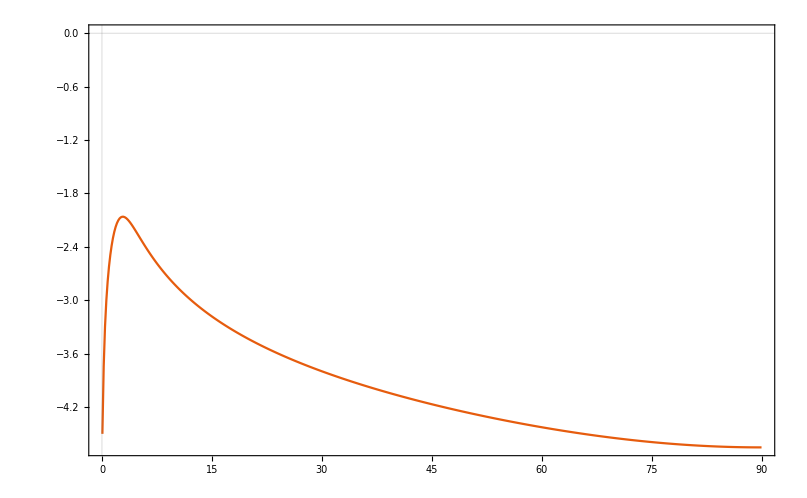

```mathematica
x=N[linearspace[0.001,π/2,500]];
y=scatter1[1,10^13,1000,5*10^6,x];
ListPlot[Transpose@{x/π*180,Log[10,y[[1]]]},Joined->True,PlotRange->All,Background->White,PlotTheme->"Scientific"]
```

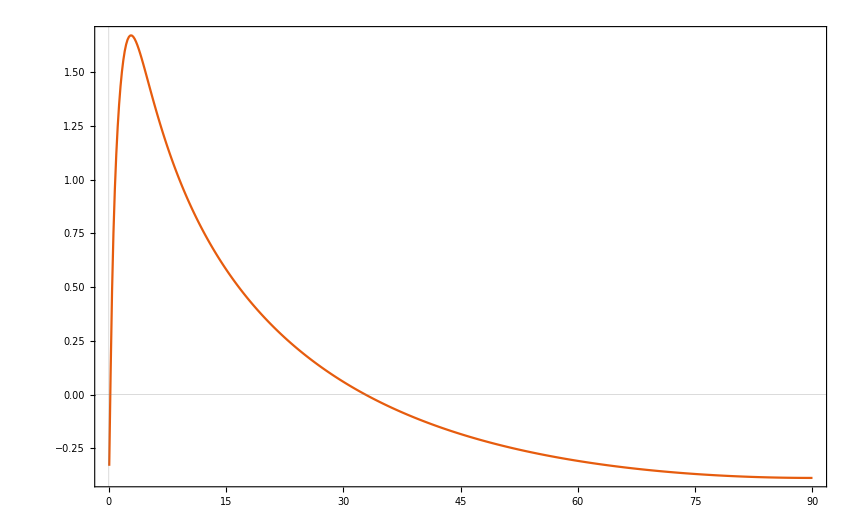

```mathematica
x=N[linearspace[0.001,π/2,500]];
y=free1[1,10^13,1000,5*10^6,x];
ListPlot[Transpose@{x/π*180,Log[10,y[[1]]]},Joined->True,PlotRange->All,Background->White,PlotTheme->"Scientific"]
```